```mathematica
(*Mathematica*)
```

```mathematica
Solve[Exp[2*Pi*I*s]-(1-Exp[6*Pi*I*s])/z^3==0,z]
```

{{z→(ⅇ^(-2 ⅈ π s)-ⅇ^(4 ⅈ π s))^(1/3)},{z→-(-1)^(1/3) (ⅇ^(-2 ⅈ π s)-ⅇ^(4 ⅈ π s))^(1/3)},{z→(-1)^(2/3) (ⅇ^(-2 ⅈ π s)-ⅇ^(4 ⅈ π s))^(1/3)}}

```mathematica
gm0=1.9796
```

1.9796

```mathematica
N[gm0]
```

1.9796

```mathematica
(*http://mathworld.wolfram.com/notebooks/Constants/LiouvillesConstant.nb*)
(*Liouville's number at 10^10*)
ϵ0=ParallelSum[10^(-n!),{n,10}]/100
v=ContinuedFraction[e0];
```

```mathematica
N[ϵ0]
```

0.00110001

```mathematica
gm=Union[Flatten[ParallelTable[gm0+p*n*ϵ0+0.00001,{n,0,20},{p,-0.5,0.5,1/20}]]];
```

```mathematica
Length[gm]
N[gm]
```

201

{1.96861,1.96916,1.96971,1.9702,1.97026,1.9707,1.97081,1.97119,1.97125,1.97136,1.97169,1.97191,1.97213,1.97218,1.97229,1.97246,1.97257,1.97268,1.97301,1.97306,1.97317,1.97334,1.97345,1.97356,1.97367,1.97383,1.97389,1.974,1.97411,1.97416,1.97422,1.97433,1.97438,1.9746,1.97466,1.97477,1.97493,1.97499,1.97515,1.97521,1.97532,1.97537,1.97543,1.97548,1.97565,1.97576,1.97587,1.97598,1.97603,1.97609,1.97614,1.97631,1.97647,1.97653,1.97658,1.97664,1.97675,1.9768,1.97686,1.97691,1.97697,1.97713,1.97719,1.9773,1.97741,1.97746,1.97752,1.97763,1.97768,1.97774,1.97779,1.97785,1.97796,1.97807,1.97812,1.97818,1.97823,1.97829,1.9784,1.97845,1.97851,1.97856,1.97862,1.97867,1.97873,1.97878,1.97884,1.97889,1.97895,1.979,1.97906,1.97911,1.97917,1.97922,1.97928,1.97933,1.97939,1.97944,1.9795,1.97955,1.97961,1.97967,1.97972,1.97978,1.97983,1.97989,1.97994,1.98,1.98005,1.98011,1.98016,1.98022,1.98027,1.98033,1.98038,1.98044,1.98049,1.98055,1.9806,1.98066,1.98071,1.98077,1.98082,1.98093,1.98099,1.98104,1.9811,1.98115,1.98126,1.98137,1.98143,1.98148,1.98154,1.98159,1.9817,1.98176,1.98181,1.98192,1.98203,1.98209,1.98225,1.98231,1.98236,1.98242,1.98247,1.98258,1.98264,1.98269,1.98275,1.98291,1.98308,1.98313,1.98319,1.98324,1.98335,1.98346,1.98357,1.98374,1.98379,1.98385,1.9839,1.98401,1.98407,1.98423,1.98429,1.98445,1.98456,1.98462,1.98484,1.98489,1.985,1.98506,1.98511,1.98522,1.98533,1.98539,1.98555,1.98566,1.98577,1.98588,1.98605,1.98616,1.98621,1.98654,1.98665,1.98676,1.98693,1.98704,1.98709,1.98731,1.98753,1.98786,1.98797,1.98803,1.98841,1.98852,1.98896,1.98902,1.98951,1.99006,1.99061}

```mathematica
f[z_]:=-z*((ⅇ^(-2 ⅈ π gm[[i]])-ⅇ^(20 ⅈ π gm[[i]]))^(1/11))+z^2
```

```mathematica
(*v=JuliaSetPoints[f[z],z,"ClosenessTolerance"->0.001];*)
```

```mathematica
tm=ParallelTable[{i,Timing[ListPlot[JuliaSetPoints[f[z],z,"ClosenessTolerance"->0.001],ImageSize->{1920,1040},PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,DisplayFunction->False];]},{i,Length[gm]}]
```

{{1,{3.0091,Null}},{2,{2.79154,Null}},{3,{3.20775,Null}},{4,{3.47663,Null}},{5,{3.46826,Null}},{6,{2.88147,Null}},{7,{2.88437,Null}},{8,{3.26065,Null}},{9,{3.11203,Null}},{10,{3.15956,Null}},{11,{3.32137,Null}},{12,{3.6084,Null}},{13,{3.83794,Null}},{14,{3.50804,Null}},{15,{3.27279,Null}},{16,{4.19322,Null}},{17,{3.87071,Null}},{18,{4.08295,Null}},{19,{4.48479,Null}},{20,{4.44107,Null}},{21,{4.30867,Null}},{22,{4.34455,Null}},{23,{3.95167,Null}},{24,{4.83033,Null}},{25,{3.94893,Null}},{26,{4.10479,Null}},{27,{4.92204,Null}},{28,{4.30193,Null}},{29,{4.16059,Null}},{30,{3.95214,Null}},{31,{3.8852,Null}},{32,{4.19648,Null}},{33,{3.99649,Null}},{34,{4.97329,Null}},{35,{4.80726,Null}},{36,{5.12086,Null}},{37,{4.50498,Null}},{38,{4.56134,Null}},{39,{6.29689,Null}},{40,{4.98058,Null}},{41,{4.77626,Null}},{42,{4.95335,Null}},{43,{4.95453,Null}},{44,{5.79385,Null}},{45,{5.08813,Null}},{46,{5.04607,Null}},{47,{5.23449,Null}},{48,{5.84315,Null}},{49,{5.56715,Null}},{50,{6.33655,Null}},{51,{6.03393,Null}},{52,{7.08836,Null}},{53,{8.49944,Null}},{54,{5.98838,Null}},{55,{6.3312,Null}},{56,{6.17724,Null}},{57,{6.17373,Null}},{58,{7.87869,Null}},{59,{7.2759,Null}},{60,{7.32826,Null}},{61,{6.38002,Null}},{62,{6.62334,Null}},{63,{9.02785,Null}},{64,{7.60056,Null}},{65,{8.26262,Null}},{66,{7.31788,Null}},{67,{8.55899,Null}},{68,{7.65809,Null}},{69,{8.2641,Null}},{70,{7.84949,Null}},{71,{7.97951,Null}},{72,{9.01953,Null}},{73,{9.93359,Null}},{74,{8.9613,Null}},{75,{9.8444,Null}},{76,{10.3454,Null}},{77,{9.96546,Null}},{78,{9.36186,Null}},{79,{12.5836,Null}},{80,{10.6278,Null}},{81,{11.7456,Null}},{82,{12.6574,Null}},{83,{12.1911,Null}},{84,{13.6805,Null}},{85,{10.6559,Null}},{86,{10.4923,Null}},{87,{11.2804,Null}},{88,{12.6931,Null}},{89,{14.4937,Null}},{90,{13.629,Null}},{91,{15.0691,Null}},{92,{16.171,Null}},{93,{16.4759,Null}},{94,{17.5996,Null}},{95,{17.6857,Null}},{96,{15.7669,Null}},{97,{23.3915,Null}},{98,{29.9737,Null}},{99,{52.3251,Null}},{100,{53.7424,Null}},{101,{73.8698,Null}},{102,{134.094,Null}},{103,{116.122,Null}},{104,{115.275,Null}},{105,{105.965,Null}},{106,{112.084,Null}},{107,{75.416,Null}},{108,{71.9488,Null}},{109,{68.9684,Null}},{110,{63.4552,Null}},{111,{63.0833,Null}},{112,{57.9471,Null}},{113,{59.9127,Null}},{114,{60.488,Null}},{115,{53.6213,Null}},{116,{48.0113,Null}},{117,{43.9798,Null}},{118,{51.5375,Null}},{119,{43.7872,Null}},{120,{38.4986,Null}},{121,{39.7926,Null}},{122,{34.9363,Null}},{123,{33.1463,Null}},{124,{31.6334,Null}},{125,{28.4636,Null}},{126,{26.9368,Null}},{127,{24.789,Null}},{128,{28.349,Null}},{129,{24.2167,Null}},{130,{26.5792,Null}},{131,{23.4872,Null}},{132,{25.2284,Null}},{133,{25.6236,Null}},{134,{24.3182,Null}},{135,{24.9346,Null}},{136,{23.7746,Null}},{137,{24.3734,Null}},{138,{24.8476,Null}},{139,{25.1872,Null}},{140,{28.0382,Null}},{141,{29.8454,Null}},{142,{30.0358,Null}},{143,{31.0726,Null}},{144,{31.9656,Null}},{145,{30.739,Null}},{146,{36.4156,Null}},{147,{35.0061,Null}},{148,{36.5174,Null}},{149,{37.4066,Null}},{150,{42.1525,Null}},{151,{52.2204,Null}},{152,{52.5007,Null}},{153,{54.3927,Null}},{154,{60.0279,Null}},{155,{68.4955,Null}},{156,{77.0866,Null}},{157,{86.0291,Null}},{158,{100.421,Null}},{159,{112.25,Null}},{160,{121.271,Null}},{161,{137.67,Null}},{162,{158.234,Null}},{163,{153.419,Null}},{164,{177.887,Null}},{165,{192.505,Null}},{166,{226.761,Null}},{167,{158.571,Null}},{168,{298.924,Null}},{169,{76.0116,Null}},{170,{18.0974,Null}},{171,{13.7265,Null}},{172,{10.8503,Null}},{173,{9.55304,Null}},{174,{6.67198,Null}},{175,{8.54464,Null}},{176,{5.66816,Null}},{177,{5.28472,Null}},{178,{4.85075,Null}},{179,{6.61901,Null}},{180,{4.43998,Null}},{181,{4.51293,Null}},{182,{4.77604,Null}},{183,{4.39414,Null}},{184,{3.54002,Null}},{185,{3.14661,Null}},{186,{2.97802,Null}},{187,{2.99185,Null}},{188,{2.52201,Null}},{189,{2.73108,Null}},{190,{2.2817,Null}},{191,{2.52975,Null}},{192,{2.60424,Null}},{193,{1.85393,Null}},{194,{2.38562,Null}},{195,{1.9415,Null}},{196,{1.88615,Null}},{197,{1.83049,Null}},{198,{1.75072,Null}},{199,{1.5223,Null}},{200,{1.59285,Null}},{201,{1.25289,Null}}}

```mathematica
lt=ParallelTable[If[tm[[i,2,1]]>30,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]
```

{{99,52.3251,1.9795},{100,53.7424,1.97955},{101,73.8698,1.97961},{102,134.094,1.97967},{103,116.122,1.97972},{104,115.275,1.97978},{105,105.965,1.97983},{106,112.084,1.97989},{107,75.416,1.97994},{108,71.9488,1.98},{109,68.9684,1.98005},{110,63.4552,1.98011},{111,63.0833,1.98016},{112,57.9471,1.98022},{113,59.9127,1.98027},{114,60.488,1.98033},{115,53.6213,1.98038},{116,48.0113,1.98044},{117,43.9798,1.98049},{118,51.5375,1.98055},{119,43.7872,1.9806},{120,38.4986,1.98066},{121,39.7926,1.98071},{122,34.9363,1.98077},{123,33.1463,1.98082},{124,31.6334,1.98093},{142,30.0358,1.98231},{143,31.0726,1.98236},{144,31.9656,1.98242},{145,30.739,1.98247},{146,36.4156,1.98258},{147,35.0061,1.98264},{148,36.5174,1.98269},{149,37.4066,1.98275},{150,42.1525,1.98291},{151,52.2204,1.98308},{152,52.5007,1.98313},{153,54.3927,1.98319},{154,60.0279,1.98324},{155,68.4955,1.98335},{156,77.0866,1.98346},{157,86.0291,1.98357},{158,100.421,1.98374},{159,112.25,1.98379},{160,121.271,1.98385},{161,137.67,1.9839},{162,158.234,1.98401},{163,153.419,1.98407},{164,177.887,1.98423},{165,192.505,1.98429},{166,226.761,1.98445},{167,158.571,1.98456},{168,298.924,1.98462},{169,76.0116,1.98484}}

```mathematica
Length[lt]
```

54

```mathematica
lt50=N[ParallelTable[If[tm[[i,2,1]]>50,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]]
```

{{99.,52.3251,1.9795},{100.,53.7424,1.97955},{101.,73.8698,1.97961},{102.,134.094,1.97967},{103.,116.122,1.97972},{104.,115.275,1.97978},{105.,105.965,1.97983},{106.,112.084,1.97989},{107.,75.416,1.97994},{108.,71.9488,1.98},{109.,68.9684,1.98005},{110.,63.4552,1.98011},{111.,63.0833,1.98016},{112.,57.9471,1.98022},{113.,59.9127,1.98027},{114.,60.488,1.98033},{115.,53.6213,1.98038},{118.,51.5375,1.98055},{151.,52.2204,1.98308},{152.,52.5007,1.98313},{153.,54.3927,1.98319},{154.,60.0279,1.98324},{155.,68.4955,1.98335},{156.,77.0866,1.98346},{157.,86.0291,1.98357},{158.,100.421,1.98374},{159.,112.25,1.98379},{160.,121.271,1.98385},{161.,137.67,1.9839},{162.,158.234,1.98401},{163.,153.419,1.98407},{164.,177.887,1.98423},{165.,192.505,1.98429},{166.,226.761,1.98445},{167.,158.571,1.98456},{168.,298.924,1.98462},{169.,76.0116,1.98484}}

```mathematica
lt200=N[ParallelTable[If[tm[[i,2,1]]>200,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]]
```

```mathematica
{{166.,226.76143,1.9844500440000001},{168.,298.923599,1.9846150455}}
```

```mathematica
(*All Timing results*)
```

```mathematica
lt0=Table[{gm[[i]],tm[[i,2,1]]},{i,Length[tm]}];
```

```mathematica
N[lt]
```

{{99.,52.3251,1.9795},{100.,53.7424,1.97955},{101.,73.8698,1.97961},{102.,134.094,1.97967},{103.,116.122,1.97972},{104.,115.275,1.97978},{105.,105.965,1.97983},{106.,112.084,1.97989},{107.,75.416,1.97994},{108.,71.9488,1.98},{109.,68.9684,1.98005},{110.,63.4552,1.98011},{111.,63.0833,1.98016},{112.,57.9471,1.98022},{113.,59.9127,1.98027},{114.,60.488,1.98033},{115.,53.6213,1.98038},{116.,48.0113,1.98044},{117.,43.9798,1.98049},{118.,51.5375,1.98055},{119.,43.7872,1.9806},{120.,38.4986,1.98066},{121.,39.7926,1.98071},{122.,34.9363,1.98077},{123.,33.1463,1.98082},{124.,31.6334,1.98093},{142.,30.0358,1.98231},{143.,31.0726,1.98236},{144.,31.9656,1.98242},{145.,30.739,1.98247},{146.,36.4156,1.98258},{147.,35.0061,1.98264},{148.,36.5174,1.98269},{149.,37.4066,1.98275},{150.,42.1525,1.98291},{151.,52.2204,1.98308},{152.,52.5007,1.98313},{153.,54.3927,1.98319},{154.,60.0279,1.98324},{155.,68.4955,1.98335},{156.,77.0866,1.98346},{157.,86.0291,1.98357},{158.,100.421,1.98374},{159.,112.25,1.98379},{160.,121.271,1.98385},{161.,137.67,1.9839},{162.,158.234,1.98401},{163.,153.419,1.98407},{164.,177.887,1.98423},{165.,192.505,1.98429},{166.,226.761,1.98445},{167.,158.571,1.98456},{168.,298.924,1.98462},{169.,76.0116,1.98484}}

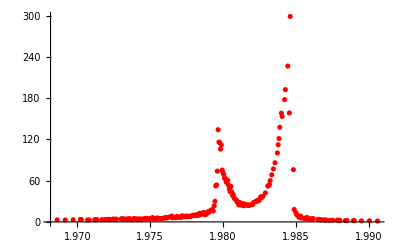

```mathematica
ListPlot[lt0,PlotStyle->Red,ImageSize->Full,PlotRange->All]
```

```mathematica
ListPointPlot3D[lt,PlotStyle->Red,ImageSize->Full]
```

-Graphics3D-

```mathematica
st=ParallelTable[If[tm[[i,2,1]]<1,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]
```

{}

```mathematica
(*end*)
```